```mathematica
gradientFieldPlot[f_,rx_,ry_,opts:OptionsPattern[]]:=Module[{img,cont,densityOptions,contourOptions,frameOptions,gradField,field,plotRangeRule,rangeCoords},densityOptions=Join[FilterRules[{opts},FilterRules[Options[DensityPlot],Except[{Prolog,Epilog,FrameTicks,PlotLabel,ImagePadding,GridLines,Mesh,AspectRatio,PlotRangePadding,Frame,Axes}]]],{PlotRangePadding->None,Frame->None,Axes->None,AspectRatio->Automatic}];
contourOptions=Join[FilterRules[{opts},FilterRules[Options[ContourPlot],Except[{Prolog,Epilog,FrameTicks,PlotLabel,Background,ContourShading,PlotRangePadding,Frame,Axes,ExclusionsStyle}]]],{PlotRangePadding->None,Frame->None,Axes->None,ContourShading->False}];
gradField=ComplexExpand[{D[f,rx[[1]]],D[f,ry[[1]]]}];
field=DensityPlot[Norm[gradField],rx,ry,Evaluate@Apply[Sequence,densityOptions]];
img=Rasterize[field,"Image"];
plotRangeRule=FilterRules[AbsoluteOptions[field],PlotRange];
cont=If[MemberQ[{0,None},(Contours/.FilterRules[{opts},Contours])],{},ContourPlot[f,rx,ry,Evaluate@Apply[Sequence,contourOptions]]];
frameOptions=Join[FilterRules[{opts},FilterRules[Options[Graphics],Except[{PlotRangeClipping,PlotRange}]]],{plotRangeRule,Frame->True,PlotRangeClipping->True}];
rangeCoords=Transpose[PlotRange/.plotRangeRule];
Apply[Show[Graphics[{Inset[Show[SetAlphaChannel[img,"ShadingOpacity"/.{opts}/.{"ShadingOpacity"->1}],AspectRatio->Full],rangeCoords[[1]],{0,0},rangeCoords[[2]]-rangeCoords[[1]]]}],cont,StreamPlot[gradField,rx,ry,Evaluate@FilterRules[{opts},StreamStyle],Evaluate@FilterRules[{opts},StreamColorFunction],Evaluate@FilterRules[{opts},StreamColorFunctionScaling],Evaluate@FilterRules[{opts},StreamPoints],Evaluate@FilterRules[{opts},StreamScale]],##]&,frameOptions]]
```

```mathematica
base=gradientFieldPlot[(y^2+(x-2)^2)^(-1/2)-(y^2+(x-1/2)^2)^(-1/2),{x,-1.5,4},{y,-1.5,1.5},PlotPoints->50,ColorFunction->"BlueGreenYellow",Contours->10,ContourStyle->White,Frame->True,FrameLabel->{"x","y"},ClippingStyle->Automatic,Axes->False,StreamStyle->Orange]
```

-Graphics-

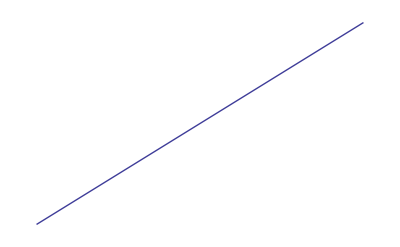

```mathematica
Plot[x,{x,0,1},Axes->False]
```

```mathematica
Epilog->Inset[Framed[Style["Spiral",20],Background->LightYellow],{Right,Bottom},{Right,Bottom}]
```

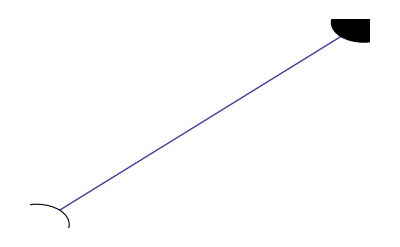

```mathematica
dipole=Plot[x-2.5, {x,3,3.5}, Epilog-> { {EdgeForm[Black],White,Disk[{3,0.5},0.05]}, Disk[{3.5,1},0.05]},Axes->False]
```

```mathematica
Show[dipole,base,PlotRange->{{-1.5,4},{-1.5,1.5}}]
```

-Graphics-